# Lección 1 - Sintaxis y Listas

Basado en el capítulo 1-7, 13 y 31 de 'An Elementary Introduction to the Wolfram Language'

## Artimética

Sumar

```mathematica
2+2
```

4

Multiplicar

```mathematica
1234*5678
```

7006652

```mathematica
1234 5678
```

7006652

Potencia

```mathematica
2^2000
```

114813069527425452423283320117768198402231770208869520047764273682576626139237031385665948631650626991844596463898746277344711896086305533142593135616665318539129989145312280000688779148240044871428926990063486244781615463646388363947317026040466353970904996558162398808944629605623311649536164221970332681344168908984458505602379484807914058900934776500429002716706625830522008132236281291761267883317206598995396418127021779858404042159853183251540889433902091920554957783589672039160081957216630582755380425583726015528348786419432054508915275783882625175435528800822842770817965453762184851149029376

Agrupar operaciones

```mathematica
9*(2+2)
```

## Introducción a listas

```mathematica
{1,2,3,4,a,b,c}
```

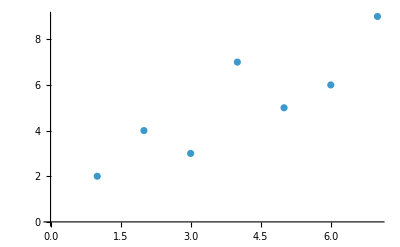

```mathematica
ListPlot[{2,4,3,7,5,6,9}]
```

Generar rangos

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

Invertir lista

```mathematica
Reverse[{1,2,3,4,5}]
```

{5,4,3,2,1}

```mathematica
Reverse[Range[20]]
```

{20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

Juntar listas

```mathematica
Join[{1,2,3}, {4,5},{6,7}]
```

{1,2,3,4,5,6,7}

```mathematica
Join[Range[3],Range[5]]
```

{1,2,3,1,2,3,4,5}

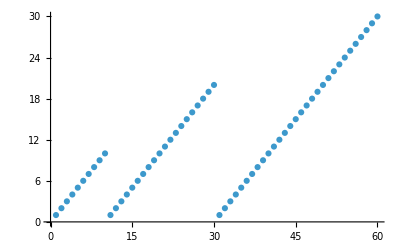

```mathematica
ListPlot[Join[Range[10],Range[20],Range[30]]]
```

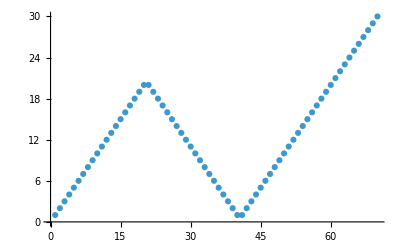

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],Range[30]]]
```

## Visualización de listas

Plots de listas

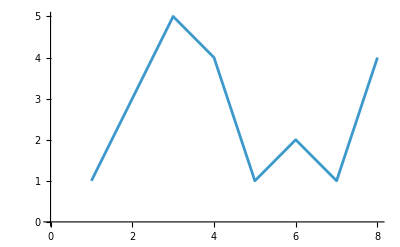

```mathematica
ListLinePlot[{1,3,5,4,1,2,1,4}]
```

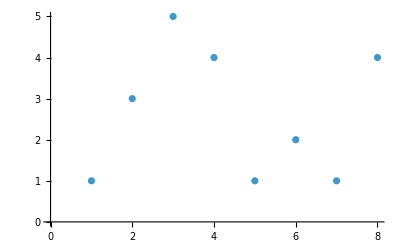

```mathematica
ListPlot[{1,3,5,4,1,2,1,4}]
```

Visualización de barras

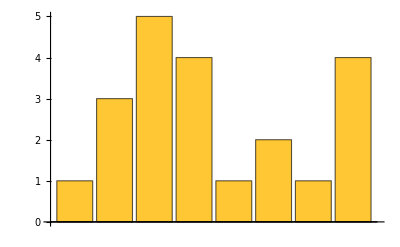

```mathematica
BarChart[{1,3,5,4,1,2,1,4}]
```

π

```mathematica
PieChart[{1,3,5,4}]
```

-Graphics-

Unidimensional

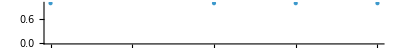

```mathematica
NumberLinePlot[{1,3,5,4}]
```

¡Los elementos en la lista puede ser lo que sea!

```mathematica
{Column[{100,350,502,400}],Row[{100,350,502,400}]}
```

{100
350
502
400,100350502400}

```mathematica
{PieChart[Range[3]],PieChart[Range[5]]}
```

{-Graphics-,-Graphics-}

## Operaciones en listas

Aritmética

```mathematica
{1,2,3}+10
```

{11,12,13}

```mathematica
{1,1,1}+{1,2,3}
```

{2,3,4}

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

Ordenamiento

```mathematica
Sort[{4,2,1,3,6}]
```

{1,2,3,4,6}

Propiedades de una lista

```mathematica
Length[{5,3,4,5,3,4,5}]
```

7

```mathematica
Total[{1,1,2,2}]
```

6

```mathematica
Count[{a,b,a,a,c,b,a},a]
```

4

```mathematica
Min[{6,7,1,2,4,5}]
```

1

```mathematica
Max[{6,7,1,2,4,5}]
```

7

```mathematica
IntegerDigits[1988]
```

{1,9,8,8}

Partes de una lista

```mathematica
First[{7,6,5}]
```

7

```mathematica
Part[{7,6,5},2]
```

6

```mathematica
{7,6,5}[[2]]
```

6

```mathematica
Take[{101,203,401,602,332,412},3]
```

{101,203,401}

```mathematica
Drop[{101,203,401,602,332,412},3]
```

{602,332,412}

## Construyendo Tables

Tables constantes

```mathematica
Table[5,10]
```

{5,5,5,5,5,5,5,5,5,5}

```mathematica
Table[x,10]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
Table[PieChart[{1,1,1}],3]
```

{-Graphics-,-Graphics-,-Graphics-}

Tables con variables

```mathematica
Table[a[n],{n,5}]
```

{a[1],a[2],a[3],a[4],a[5]}

```mathematica
Table[n+1,{n,1,10}]
```

{2,3,4,5,6,7,8,9,10,11}

```mathematica
Table[Range[n],{n,5}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

```mathematica
Table[Column[Range[n]],{n,8}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

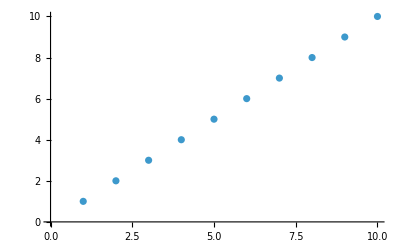
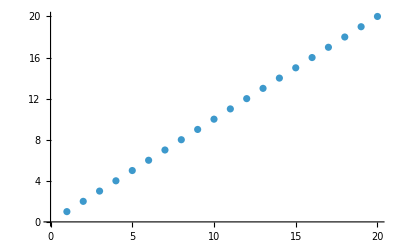
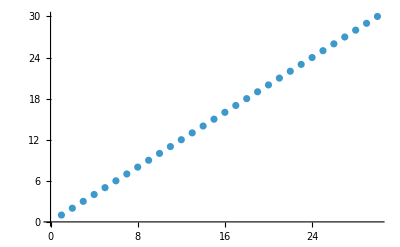

```mathematica
Table[ListPlot[Range[10*n]],{n,3}]
```

Control del iterador

```mathematica
Table[f[n],{n,4,10}]
```

{f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Table[f[n],{n,4,10,2}]
```

{f[4],f[6],f[8],f[10]}

```mathematica
Table[RandomInteger[10],{20}]
```

{8,9,9,7,4,3,8,3,3,5,1,1,7,9,1,2,5,2,5,3}

```mathematica
RandomInteger[10,20]
```

{2,8,0,7,3,9,9,10,0,3,1,2,0,10,2,10,4,8,1,10}

## Arrays (Listas de listas)

Arrays constantes

```mathematica
Table[x,4]
```

{x,x,x,x}

```mathematica
Table[x,4,5]
```

{{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x}}

```mathematica
Grid[Table[x,4,5]]
```

x | x | x | x | x
x | x | x | x | x
x | x | x | x | x
x | x | x | x | x

Arrays con iteradores

```mathematica
Grid[Table[RGBColor[r,0,b],{r,0,1,.2},{b,0,1,.2}]]
```

RGBColor[0., 0, 0.] | RGBColor[0., 0, 0.2] | RGBColor[0., 0, 0.4] | RGBColor[0., 0, 0.6000000000000001] | RGBColor[0., 0, 0.8] | RGBColor[0., 0, 1.]
RGBColor[0.2, 0, 0.] | RGBColor[0.2, 0, 0.2] | RGBColor[0.2, 0, 0.4] | RGBColor[0.2, 0, 0.6000000000000001] | RGBColor[0.2, 0, 0.8] | RGBColor[0.2, 0, 1.]
RGBColor[0.4, 0, 0.] | RGBColor[0.4, 0, 0.2] | RGBColor[0.4, 0, 0.4] | RGBColor[0.4, 0, 0.6000000000000001] | RGBColor[0.4, 0, 0.8] | RGBColor[0.4, 0, 1.]
RGBColor[0.6000000000000001, 0, 0.] | RGBColor[0.6000000000000001, 0, 0.2] | RGBColor[0.6000000000000001, 0, 0.4] | RGBColor[0.6000000000000001, 0, 0.6000000000000001] | RGBColor[0.6000000000000001, 0, 0.8] | RGBColor[0.6000000000000001, 0, 1.]
RGBColor[0.8, 0, 0.] | RGBColor[0.8, 0, 0.2] | RGBColor[0.8, 0, 0.4] | RGBColor[0.8, 0, 0.6000000000000001] | RGBColor[0.8, 0, 0.8] | RGBColor[0.8, 0, 1.]
RGBColor[1., 0, 0.] | RGBColor[1., 0, 0.2] | RGBColor[1., 0, 0.4] | RGBColor[1., 0, 0.6000000000000001] | RGBColor[1., 0, 0.8] | RGBColor[1., 0, 1.]

```mathematica
Grid[Table[i,{i,4},{j,5}]]
```

1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4

```mathematica
Grid[Table[j,{i,4},{j,5}]]
```

1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5

```mathematica
Grid[Table[i+j,{i,5},{j,5}]]
```

2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9
6 | 7 | 8 | 9 | 10

```mathematica
Grid[Table[i*j,{i,5},{j,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

```mathematica
Grid[Table[Subscript[a, i,j],{i,5},{j,5}]]
```

a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5)
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5)

Representanción gráfica

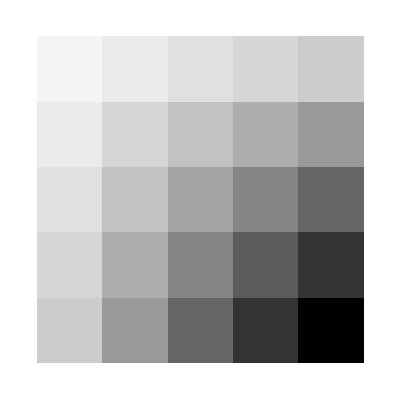

```mathematica
ArrayPlot[Table[i*j,{i,5},{j,5}]]
```

```mathematica
ArrayPlot[Table[RandomInteger[10],30,30]]
```

-Graphics-

Aritmética

```mathematica
1-{0,1,1}
```

{1,0,0}

```mathematica
RandomInteger[12,{3,4}]-RandomInteger[22,{3,4}]
```

{{-9,7,-3,-12},{8,-8,8,-18},{2,-6,2,-5}}

```mathematica
MatrixForm[%]
```

(-9 | 7 | -3 | -12
8 | -8 | 8 | -18
2 | -6 | 2 | -5)

## Parts of Lists

Sintaxis

```mathematica
Part[{a,b,c,d,e,f,g},2]
```

b

```mathematica
{a,b,c,d,e,f,g}[[2]]
```

b

Índices negativos

```mathematica
{a,b,c,d,e,f,g}[[-2]]
```

f

Varios elementos

```mathematica
{a,b,c,d,e,f,g}[[{2,4,5}]]
```

{b,d,e}

Secuencia de elementos

```mathematica
{a,b,c,d,e,f,g}[[2;;5]]
```

{b,c,d,e}

```mathematica
Take[{a,b,c,d,e,f,g},4]
```

{a,b,c,d}

```mathematica
TakeLargest[Range[20],5]
```

{20,19,18,17,16}

```mathematica
TakeLargestBy[Array[RomanNumeral,100],StringLength,5]
```

{LXXXVIII,XXXVIII,LXXVIII,LXXXIII,LXXXVII}

Selección en diferentes niveles

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2,1]]
```

d

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[All,1]]
```

{a,d,g}

Posición de elementos

```mathematica
Position[{{a,b,c},{d,e,f},{g,h,i}},d]
```

{{2,1}}

```mathematica
Position[{{x,y,x},{y,y,x},{x,y,y},{x,x,y}},x]
```

{{1,1},{1,3},{2,3},{3,1},{4,1},{4,2}}

```mathematica
Position[Characters["The Wolfram Language"],"a"]
```

{{10},{14},{18}}

```mathematica
Flatten[Position[IntegerDigits[2^500],0]]
```

{7,9,19,20,44,47,50,65,75,88,89,96,103,115,116,119,120,137}

## Tarea

Realizar los ejercicios correspondientes a los capitulos 1-7, 13 y 31.

Revisar la documentación y ejemplos de la función Partition.